## Brian — PS 2 — 2025-01-21 — Solution

## Exercises from EIWL3 Section 5

```mathematica
Reverse[Range[10]^2] (* I could square and reverse. *)
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
Reverse[Range[10]]^2 (* Or I could get the exact same thing by reversing and then squaring. *)
```

{100,81,64,49,36,25,16,9,4,1}

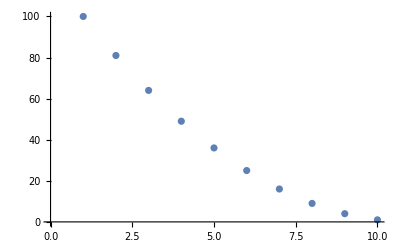

```mathematica
ListPlot[Reverse[Range[10]]^2 ]
```

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

```mathematica
Range[10,20,1] (* Range[10, 20, 1] is simpler and clearer than Range[11] + 9 but it doesn't use plus, and for some reason, Wolfram requested we use plus *)
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Sort[Join[Range[5]^2, Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

```mathematica
Length[IntegerDigits[2^128]]
```

39

```mathematica
First[IntegerDigits[2^32]]
```

4

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Max[IntegerDigits[2^20]]
```

8

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

```mathematica
Sort[IntegerDigits[2^20]][[0]] (* I am using a special notation for Part *)
```

{0,1,4,5,6,7,8}

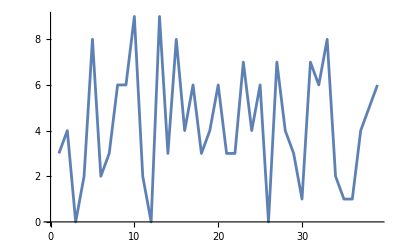

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

```mathematica
Drop[Take[Range[100],20],10]
```

{11,12,13,14,15,16,17,18,19,20}

## Exercises from EIWL3 Section 6

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

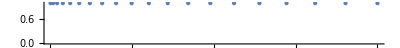

```mathematica
NumberLinePlot[Table[n^2,{n,1,20}]]
```

```mathematica
Table[i,{i,2,20,2}] (* I assume he wants us to keep using Table, but there are lots of other ways of doing this *)
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

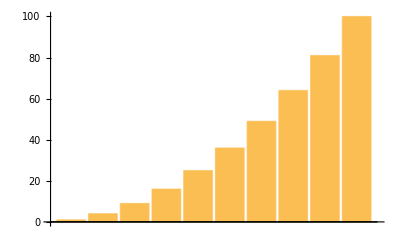

```mathematica
BarChart[Table[i^2,{i,1,10}]]
```

```mathematica
Table[IntegerDigits[i^2],{i,1,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

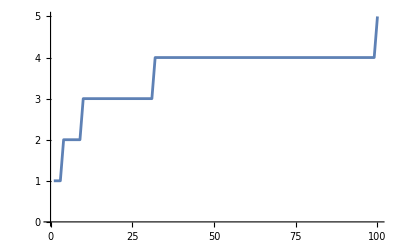

```mathematica
ListLinePlot[Table[Length[IntegerDigits[i^2]],{i,1,100}]]
```

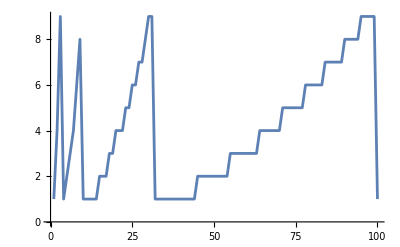

```mathematica
ListLinePlot[Table[First[IntegerDigits[i^2]],{i,1,100}]]
```

## Exercises from EIWL3 Section 7

```mathematica
{Red,Yellow,Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Column[{Red,Yellow,Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

```mathematica
ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

```mathematica
Table[Hue[i],{i,0,1,0.05}]
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
Blend[{Pink,Yellow}]
```

RGBColor[1, 0.75, 0.25]

```mathematica
Table[Blend[{Hue[i],Yellow}],{i,0,1,0.05}]
```

{RGBColor[1., 0.5, 0.],RGBColor[1., 0.65, 0.],RGBColor[1., 0.8, 0.],RGBColor[1., 0.9500000000000001, 0.],RGBColor[0.8999999999999999, 1., 0.],RGBColor[0.75, 1., 0.],RGBColor[0.5999999999999999, 1., 0.],RGBColor[0.5, 1., 0.050000000000000044],RGBColor[0.5, 1., 0.20000000000000018],RGBColor[0.5, 1., 0.3500000000000001],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 0.8499999999999999, 0.5],RGBColor[0.5, 0.6999999999999997, 0.5],RGBColor[0.5, 0.5499999999999998, 0.5],RGBColor[0.6000000000000001, 0.5, 0.5],RGBColor[0.75, 0.5, 0.5],RGBColor[0.9000000000000004, 0.5, 0.5],RGBColor[1., 0.5, 0.44999999999999973],RGBColor[1., 0.5, 0.2999999999999998],RGBColor[1., 0.5, 0.1499999999999999],RGBColor[1., 0.5, 0.]}

```mathematica
Table[Style[i,Hue[i]],{i,0.0,1.0,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Style[Purple,100]
```

RGBColor[0.5, 0, 0.5]

```mathematica
Table[Style[Red,i],{i,10,100,10}]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
Style[999,Red,100]
```

999

```mathematica
Table[Style[i,i],{i,Range[10]^2}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
{Red,Yellow,Green}[[RandomInteger[2,100]+1]]
```

{RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
Table[Style[i,3i],{i,Take[IntegerDigits[2^1000],50]}]
```

{1,0,7,1,5,0,8,6,0,7,1,8,6,2,6,7,3,2,0,9,4,8,4,2,5,0,4,9,0,6,0,0,0,1,8,1,0,5,6,1,4,0,4,8,1,1,7,0,5,5}

## Exercises from EIWL3 Section 8



```mathematica
Graphics[RegularPolygon[3]]
```

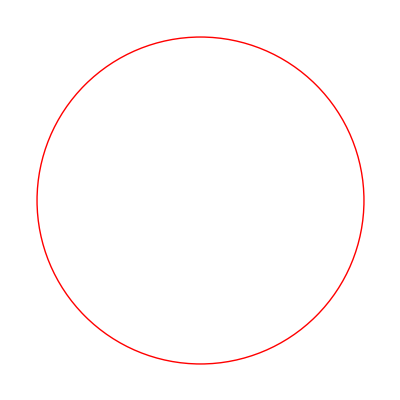

```mathematica
Graphics[Style[Circle[],Red]]
```

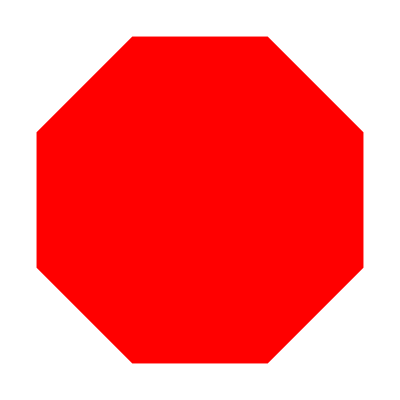

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```


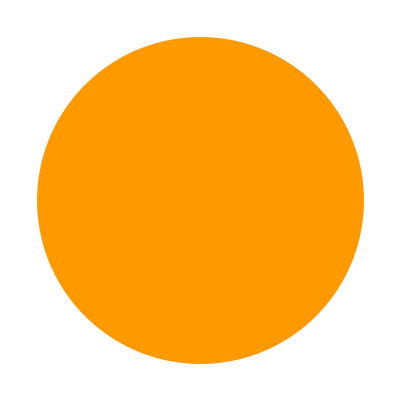
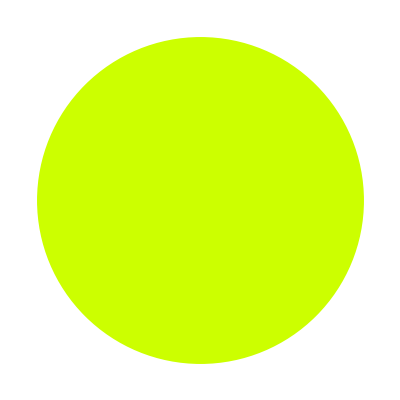
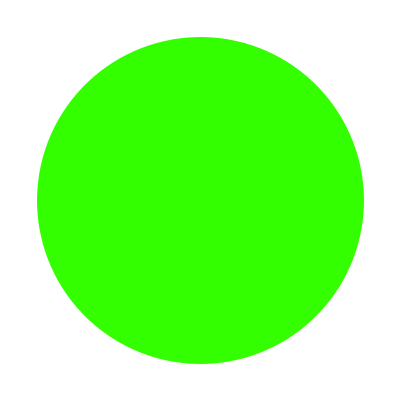
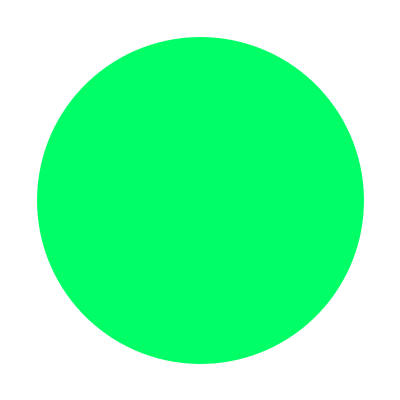
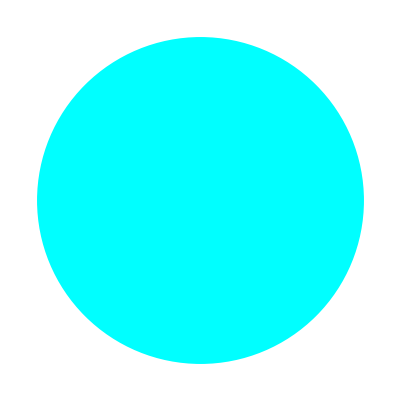
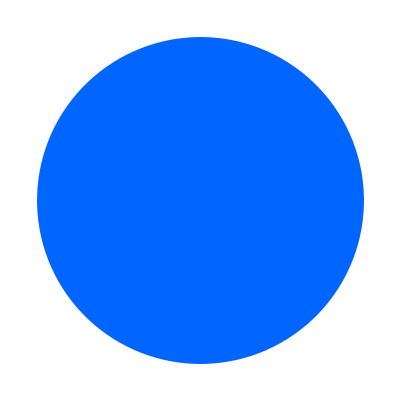
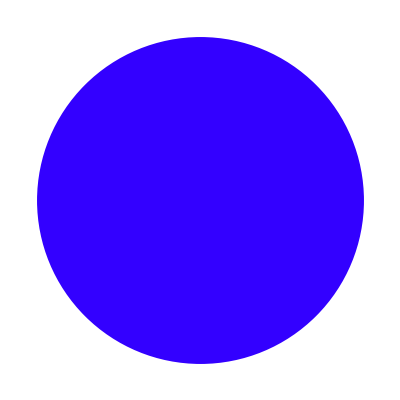
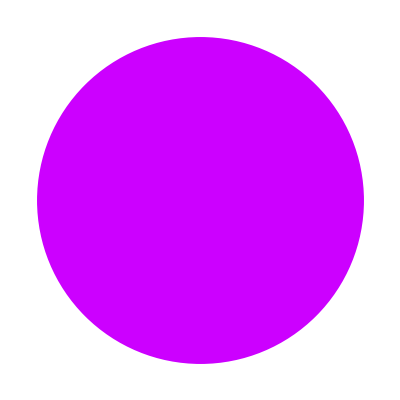
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[],Hue[i]]],{i,0.0,1.0,0.1}]
```

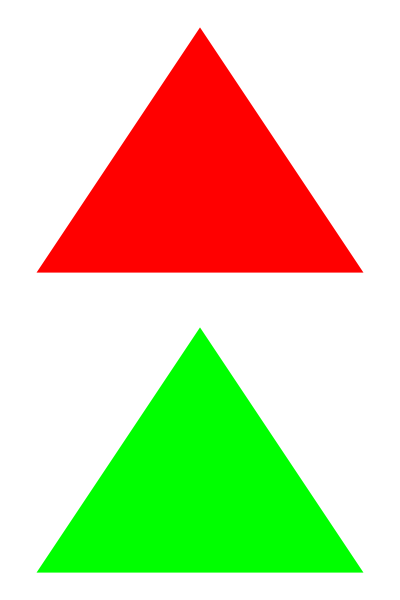

```mathematica
Column[{
Graphics[Style[RegularPolygon[3],Red]],
Graphics[Style[RegularPolygon[3],Green]]
}] (* The nested brackets and braces got deep enough that I used indenting to help me get it right. *)
```

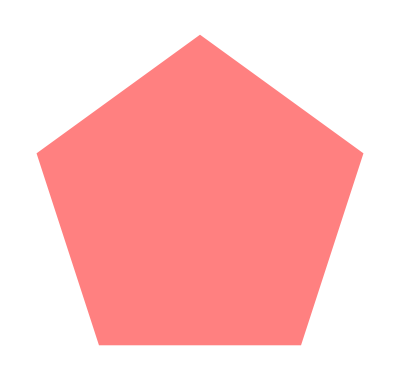
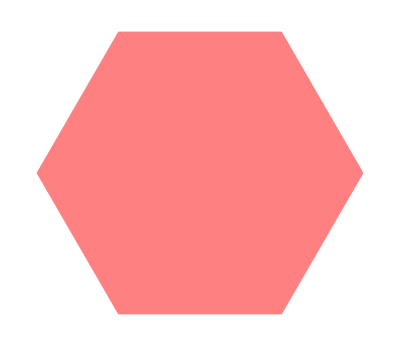
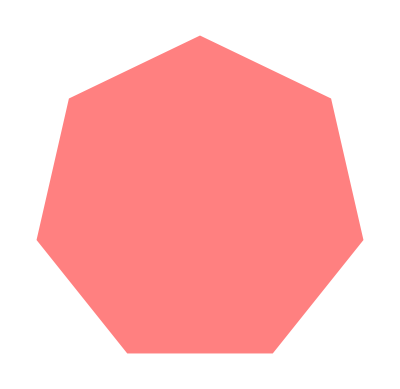
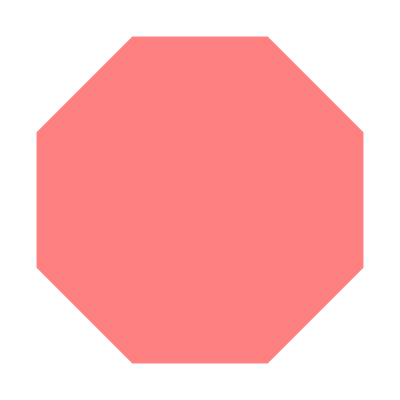
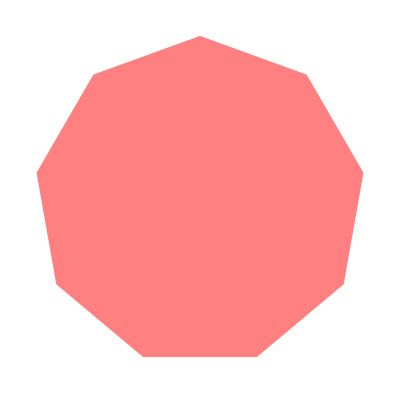
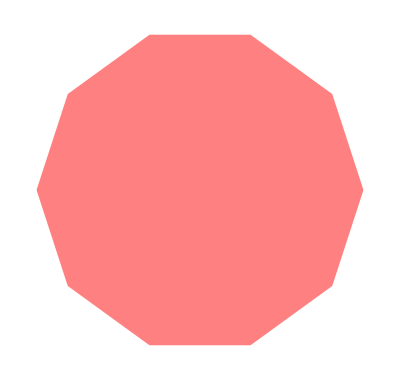

```mathematica
Table[Graphics[Style[RegularPolygon[i],Pink]],{i,5,10}]
```

```mathematica
Graphics3D[Style[Cylinder[],Purple]]
```

-Graphics3D-

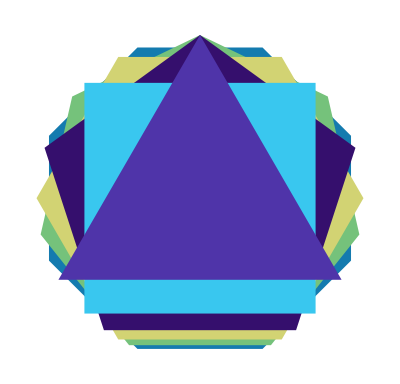

```mathematica
Graphics[Table[
Style[RegularPolygon[i],RandomColor[]],
{i,8,3,-1}
]]
```